# Higgs to Zγ via a stop loop (off-shell, with mixing) - attempt 1 with the FeynArts pipeline

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
<<FeynArts`
<<FormCalc`
```

FeynArts 3.10 (11 Jul 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

## Diagram Creation

> Top. 1 ad/becf/dedfef.m, 1 diagram

> Top. 2 ad/bece/dede.m, 1 diagram

> Top. 3 ad/becd/eded.m, 1 diagram

> Top. 4 ad/bdce/eded.m, 1 diagram

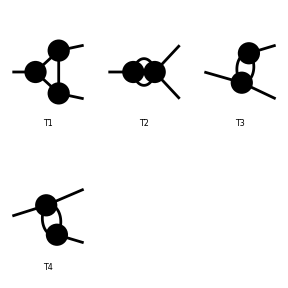

```mathematica
topo1=CreateTopologies[1,1->2,ExcludeTopologies->{Internal}];
Paint[topo1];
```

loading generic model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/MSSM.mod

> 94 particles (incl. antiparticles) in 23 classes

> $CounterTerms are ON

> 383 vertices

classes model {MSSM} initialized

Excluding 0 Generic, 31 Classes, and 72 Particles fields

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 8 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 0 Generic, 31 Classes, and 72 Particles fields

Restoring 18 field point(s)

in total: 12 Particles insertions

> Top. 1 ad/becf/dedfef.m, 8 diagrams

> Top. 2 ad/bece/dede.m, 4 diagrams

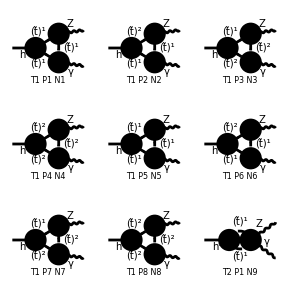

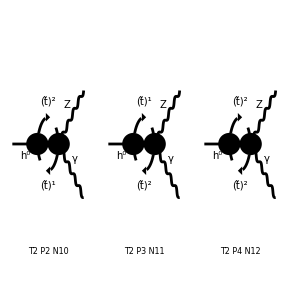

```mathematica
diag1=InsertFields[topo1,{S[1]}->{V[2],V[1]},InsertionLevel->{Particles},Model->"MSSM",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2],S[11],S[12],S[13,{1,1}],S[13,{2,1}],S[13,{1,2}],S[13,{2,2}],S[14],S[3],S[4],S[5],S[6],F[11],F[12],F[3],U[1],U[2],U[3],U[4]},Restrictions->NoLightFHCoupling];
Paint[diag1];
```

## Generate Amplitude

```mathematica
ClearProcess[];
amp=CalcFeynAmp[OffShell[CreateFeynAmp[diag1],2-> mg1,3-> mg2],FermionChains->Chiral]//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 8 Particles amplitudes

> Top. 2: 4 Particles amplitudes

in total: 12 Particles amplitudes

preparing FORM code in /home/paul/projects/physics/Research/fc-amp-1.frm

running FORM...

ok

Amp((S(1) | k(1) | Mh0 | {})→(V(2) | k(2) | mg1 | {}
V(1) | k(3) | mg2 | {}))(-1/(36 π CW2 MW SB SW2)Alfa EL (Pair1 (Sub1 Sub6 B0i(bb0,Mh02,MSf2(1,3,3),MSf2(1,3,3))+Sub11 Sub7 B0i(bb0,Mh02,MSf2(2,3,3),MSf2(2,3,3))+(Sub12 Sub13+Sub14 Sub15) B0i(bb0,Mh02,MSf2(1,3,3),MSf2(2,3,3))-4 Sub1 Sub6 C0i(cc00,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))-4 Sub11 Sub7 C0i(cc00,mg1^2,mg2^2,Mh02,MSf2(2,3,3),MSf2(2,3,3),MSf2(2,3,3)))-2 (Sub12 Sub13+Sub14 Sub15) (Pair1 C0i(cc00,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(2,3,3),MSf2(2,3,3))+Pair1 C0i(cc00,mg2^2,Mh02,mg1^2,MSf2(1,3,3),MSf2(1,3,3),MSf2(2,3,3))-Pair2 Pair3 C0i(cc12,mg2^2,Mh02,mg1^2,MSf2(1,3,3),MSf2(1,3,3),MSf2(2,3,3)))+2 Pair2 Pair3 (-2 Sub1 Sub6 (C0i(cc12,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))+C0i(cc2,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))+C0i(cc22,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3)))-2 Sub11 Sub7 (C0i(cc12,mg1^2,mg2^2,Mh02,MSf2(2,3,3),MSf2(2,3,3),MSf2(2,3,3))+C0i(cc2,mg1^2,mg2^2,Mh02,MSf2(2,3,3),MSf2(2,3,3),MSf2(2,3,3))+C0i(cc22,mg1^2,mg2^2,Mh02,MSf2(2,3,3),MSf2(2,3,3),MSf2(2,3,3)))-(Sub12 Sub13+Sub14 Sub15) (C0i(cc12,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(2,3,3),MSf2(2,3,3))+C0i(cc2,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(2,3,3),MSf2(2,3,3))+C0i(cc22,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(2,3,3),MSf2(2,3,3))))))

#### Check divergent piece

```mathematica
uvcheck=UVDivergentPart[expr]//Simplify;
FreeQ[uvcheck,Divergence]
```

True

```mathematica
UVDivergentPart[amp]//Simplify
divergence=%[[1]]
```

Amp((S(1) | k(1) | Mh0 | {})→(V(2) | k(2) | mg1 | {}
V(1) | k(3) | mg2 | {}))(0)

0

#### Prepare for looptools

```mathematica
squ=SquaredME[amp];
(* If contains Fermion *)
(*** Don't forget to multiply for FINAL fermions. ***)
squ=(1(squ[[1]]//.squ[[2]]))//.HelicityME[amp]//.{Hel[_]->0}; (* or simply with _Hel=0 *)
(* If contains Colored Particles *)
(*** Don't forget to divide for INITIAL colored particles. ***)

squ=(squ//.ColourME[amp])/1;
(* If contains Vector *)
(*** Don't forget to divide for initial vectors. ***)

mat= PolarizationSum[squ,GaugeTerms->False]/1;  (*Asserting gauge invariance! *)
```

HelicityME::nomat: Warning: No matrix elements to compute.

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /home/paul/projects/physics/Research/fc-pol-4.frm

running FORM...

ok

Note: polarization sum auto squares the matrix element. Subexpr seems to destroy this line.

```mathematica
(*mat=PolarizationSum[amp,GaugeTerms->False]//.Subexpr[]//.Abbr[]//Simplify*)
```

# Input point

## Inputs

```mathematica
stopM1 = 1000;
stopM2 = 1500;
mixT = 300;
muM = 250;
betaA = 1.47; (*tan beta = 10*)
alphaA = betaA - (Pi/2);
offM1 =91.2;
offM2 = 22;
Clear[matSq,c1,c2,ghSS,h11,h12,h22,z11,z12,z22,m,mh,mZ,mW]
```

# FeynArts Evaluation

## Numerical Evaluation

```mathematica
matPostSub = mat//.Subexpr[]//. mg1 -> offM1 //.mg2-> offM2
```

(Alfa Alfa2 ((1-((USf(2,1,3,3) (1)+1) (1)+1) 1)/1296+1/1296))/(CW2^2 MW2 π SB2 SW2^2)
 |  |  |  |

```mathematica
Install["LoopTools"]
```

LinkObject[…]

```mathematica
VALUES[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:={
Den[p2_,m2_]:>1/(p2-m2),
MT->173,MT2->173^2,
MW->80.4,MW2->80.4^2,
MZ-> 91.2,MZ2-> (91.2)^2,
Mh0-> 125,Mh02->(125)^2,
Alfa->1/128,Alfa2->1/128^2,
SW2->0.23,CW-> (MW/MZ),CW2->(MW/MZ)^2,
α-> alpha,β-> beta,MUE-> mu,MUEC-> mu,
CA->Cos[α],SB->Sin[β],SA->Sin[α],
SB2->(Sin[β])^2,SAB->Sin[α+β],
thetat-> (1/2)(ArcSin[(-2*MT*xt)/(stopMass2^2-stopMass1^2)]),
MSf[1,3,x_]->stopMass1,MSf2[1,3,x_]->stopMass1^2,
MSf[2,3,x_]->stopMass2,MSf2[2,3,x_]->stopMass2^2,
Af[3,3,3]-> ((xt/(MT))+MUE*Cot[β]),AfC[3,3,3]-> ((xt/(MT))+MUE*Cot[β]),
USfC[x_,y_,3,3]-> USf[x,y,3,3],USf[1,1,3,3]->Cos[thetat] ,USf[1,2,3,3]->Sin[thetat],USf[2,1,3,3]-> -Sin[thetat],USf[2,2,3,3]-> Cos[thetat]}
MyMatrixElement[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:=matPostSub//.VALUES[stopMass1,stopMass2,xt,mu,alpha,beta]//Simplify
```

```mathematica
feynArtsResult =Chop[MyMatrixElement[stopM1,stopM2,mixT,muM,alphaA,betaA]]
```

9.61901×10^-8

```mathematica
(*LogLogPlot[{MyMatrixElement[ms,10000,0,250,0,1.47]},{ms,200,1000}]*)
```

## Definitions and terminology

Notation for the diphoton decay:
p1= Momentum of 1st out-going particle (Z or photon)
p2= Momentum of 2nd out-going particle (photon)
mh= Mass of the decaying higgs
m = Mass of the stop
ghss= Higgs-stop coupling
α = Fine structure constant
x and y are Feynman parameters

Additional notation for the Zγ decay:
m1= Mass of the lighter stop mass eignestate
m2= Mass of the heavier stop mass eigenstate
zij= Coupling of the Z boson to stops of mass eigenstates ij = 11, 12, 21, 22
zgij= 4 point coupling of the Z boson and a photon to the stop mass eigenstates
hij= Higgs coupling to stops in their mass eigenstates (note: h11= ghSS)

After introducing all LO and NLO coefficients in this language, I will introduce the explicit dependence of these factors on MSSM parameters. See my summary Latex document for more details.

## Higgs to Zγ (off-shell, mixed)

```mathematica
matSq =Times[Rational[9,2],Plus[Times[Power[c2,2],Plus[Power[mg1,4],Times[Power[mg1,2],Plus[Times[4,Power[mg2,2]],Times[-2,Power[mh,2]]]],Power[Plus[Power[mg2,2],Times[-1,Power[mh,2]]],2]]],Times[6,c1,c2,Plus[Power[mg1,2],Power[mg2,2],Times[-1,Power[mh,2]]],Power[mZ,2]],Times[8,Power[c1,2],Power[mZ,4]]],Power[v,-2]](*Colour factors and polarization sums have already been taken into consideration - see matrix element squared file for details*)
```

(9 (8 c1^2 mZ^4+6 c1 c2 mZ^2 (mg1^2+mg2^2-mh^2)+c2^2 (mg1^4+mg1^2 (4 mg2^2-2 mh^2)+(mg2^2-mh^2)^2)))/(2 v^2)

The c1 on-shell term is zero.

```mathematica
c1LOzgMixInted =2*Times[M2,Power[mZ,-2],v,Plus[Times[Rational[-1,6],e,h11,Power[mh,-1],mZ,Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-3],Power[Pi,-2],z11,Plus[Times[4,Power[mh,2],Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[1,2]],mZ,ArcTan[Times[mh,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]]],Times[2,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[1,2]],Power[mZ,3],ArcTan[Times[mh,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]]],Times[Power[mh,3],Plus[Times[-2,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[1,2]],ArcTan[Times[mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]]],Times[mZ,Plus[-3,Power[ArcTan[Times[mh,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]],2],Times[-1,Power[ArcTan[Times[mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]],2]]]]]],Times[mh,mZ,Plus[Times[-4,mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[1,2]],ArcTan[Times[mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]]],Times[4,Power[m1,2],Plus[Power[ArcTan[Times[mh,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]],2],Times[-1,Power[ArcTan[Times[mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]],2]]]],Times[Power[mZ,2],Plus[3,Power[ArcTan[Times[mh,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]],2],Times[-1,Power[ArcTan[Times[mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]],2]]]]]]]],Times[Rational[-1,6],e,Power[h22,2],Power[mh,-1],mZ,Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-3],Power[Pi,-2],Plus[Times[4,Power[mh,2],Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mh,2]]],Rational[1,2]],mZ,ArcTan[Times[mh,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]]],Times[2,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mh,2]]],Rational[1,2]],Power[mZ,3],ArcTan[Times[mh,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]]],Times[Power[mh,3],Plus[Times[-2,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mZ,2]]],Rational[1,2]],ArcTan[Times[mZ,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]]],Times[mZ,Plus[-3,Power[ArcTan[Times[mh,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]],2],Times[-1,Power[ArcTan[Times[mZ,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]],2]]]]]],Times[mh,mZ,Plus[Times[-4,mZ,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mZ,2]]],Rational[1,2]],ArcTan[Times[mZ,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]]],Times[4,Power[m2,2],Plus[Power[ArcTan[Times[mh,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]],2],Times[-1,Power[ArcTan[Times[mZ,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]],2]]]],Times[Power[mZ,2],Plus[3,Power[ArcTan[Times[mh,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]],2],Times[-1,Power[ArcTan[Times[mZ,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]],2]]]]]]]],Times[Rational[-1,48],e,h12,Power[mh,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-3],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Power[Pi,-2],z12,Plus[Times[-1,Power[mh,8],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],Plus[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Times[12,Plus[Times[-1,Power[m1,2]],Power[m2,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-16,Power[mZ,2],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]]]],Times[2,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Power[mZ,4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],Plus[Times[2,Plus[Times[-1,Power[m1,2]],Power[m2,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Log[Power[m1,2]]]]],Times[-2,Power[mh,2],Power[mZ,2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],Plus[Times[4,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Plus[Times[2,Plus[Times[-1,Power[m1,2]],Power[m2,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Log[Power[m1,2]]]]],Times[Power[mZ,2],Plus[Times[8,Power[m1,2],Plus[Times[-1,Power[m1,2]],Power[m2,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Plus[Times[-3,Power[m1,2]],Power[m2,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Log[Power[m1,2]]]]]]],Times[-2,Power[mh,6],Plus[Times[4,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[4,Power[mZ,4],Plus[Times[-1,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],Plus[Times[12,Plus[Power[m1,4],Times[-1,Power[m2,4]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Plus[Times[6,Power[m1,2]],Times[-5,Power[m2,2]],Times[Plus[Times[3,Power[m1,2]],Times[-2,Power[m2,2]]],Log[Power[m1,2]]],Times[Plus[Times[2,Power[m1,2]],Times[-1,Power[m2,2]]],Log[Power[m1,2]]]]]]],Times[Power[mZ,2],Plus[Times[-8,Plus[Power[m1,2],Power[m2,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],Plus[Times[4,Plus[Power[m1,2],Times[3,Power[m2,2]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Plus[2,Log[Power[m1,2]]]]]]]]]],Times[Power[mh,4],Plus[Times[-16,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Power[mZ,6],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[6,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Plus[Times[4,Plus[Times[-1,Power[m1,2]],Power[m2,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],Plus[Times[2,Plus[Times[-1,Power[m1,2]],Power[m2,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Log[Power[m1,2]]]]]]],Times[Power[mZ,4],Plus[Times[8,Plus[Power[m1,2],Times[7,Power[m2,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],Plus[Times[-4,Plus[Times[5,Power[m1,2]],Times[3,Power[m2,2]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Plus[9,Times[4,Log[Power[m1,2]]]]]]]]],Times[-2,Power[mZ,2],Plus[Times[16,Plus[Times[-1,Power[m1,4]],Times[-1,Power[m1,2],Power[m2,2]],Times[2,Power[m2,4]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],Plus[Times[8,Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Plus[Times[-6,Power[m1,2]],Times[5,Power[m2,2]],Times[Power[m1,2],Log[Power[m1,2]]],Times[Plus[Times[-3,Power[m1,2]],Times[2,Power[m2,2]]],Log[Power[m1,2]]]]]]]]]]]]],Times[Rational[-1,48],e,h12,Power[mh,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-3],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Power[Pi,-2],z12,Plus[Times[-1,Power[mh,8],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],Plus[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Times[12,Plus[Power[m1,2],Times[-1,Power[m2,2]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-16,Power[mZ,2],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]]]],Times[2,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Power[mZ,4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],Plus[Times[2,Plus[Power[m1,2],Times[-1,Power[m2,2]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Log[Power[m2,2]]]]],Times[-2,Power[mh,2],Power[mZ,2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],Plus[Times[4,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Plus[Times[2,Plus[Power[m1,2],Times[-1,Power[m2,2]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Log[Power[m2,2]]]]],Times[Power[mZ,2],Plus[Times[8,Power[m2,2],Plus[Power[m1,2],Times[-1,Power[m2,2]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Plus[Power[m1,2],Times[-3,Power[m2,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Log[Power[m2,2]]]]]]],Times[-2,Power[mh,6],Plus[Times[4,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[4,Power[mZ,4],Plus[Times[-1,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],Plus[Times[-12,Plus[Power[m1,4],Times[-1,Power[m2,4]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Plus[Times[-5,Power[m1,2]],Times[6,Power[m2,2]],Times[-1,Plus[Power[m1,2],Times[-2,Power[m2,2]]],Log[Power[m2,2]]],Times[Plus[Times[-2,Power[m1,2]],Times[3,Power[m2,2]]],Log[Power[m2,2]]]]]]],Times[Power[mZ,2],Plus[Times[-8,Plus[Power[m1,2],Power[m2,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],Plus[Times[4,Plus[Times[3,Power[m1,2]],Power[m2,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Plus[2,Log[Power[m2,2]]]]]]]]]],Times[Power[mh,4],Plus[Times[-16,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Power[mZ,6],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[6,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Plus[Times[4,Plus[Power[m1,2],Times[-1,Power[m2,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],Plus[Times[2,Plus[Power[m1,2],Times[-1,Power[m2,2]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Log[Power[m2,2]]]]]]],Times[Power[mZ,4],Plus[Times[8,Plus[Times[7,Power[m1,2]],Power[m2,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],Plus[Times[-4,Plus[Times[3,Power[m1,2]],Times[5,Power[m2,2]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Plus[9,Times[4,Log[Power[m2,2]]]]]]]]],Times[-2,Power[mZ,2],Plus[Times[16,Plus[Times[2,Power[m1,4]],Times[-1,Power[m1,2],Power[m2,2]],Times[-1,Power[m2,4]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],Plus[Times[8,Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],Plus[Times[5,Power[m1,2]],Times[-6,Power[m2,2]],Times[Power[m2,2],Log[Power[m2,2]]],Times[Plus[Times[2,Power[m1,2]],Times[-3,Power[m2,2]]],Log[Power[m2,2]]]]]]]]]]]]],Times[Rational[1,24],e,h12,Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-3],Power[Pi,-2],z12,Plus[Times[-2,Power[m1,2],Plus[Power[mh,2],Times[-1,Power[mZ,2]]]],Times[-1,Plus[Times[-4,Power[m1,2]],Times[4,Power[m2,2]],Power[mh,2],Times[-11,Power[mZ,2]]],Plus[Power[mh,2],Times[-1,Power[mZ,2]]]],Times[Rational[1,2],Plus[Power[mh,4],Times[-8,Power[mh,2],Power[mZ,2]],Times[7,Power[mZ,4]]]],Times[Rational[1,2],Power[m1,2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[mh,2],Plus[-4,Log[Power[m2,2]]]],Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]]]],Times[Rational[-9,2],Power[m1,2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[mZ,2],Plus[-4,Log[Power[m2,2]]]],Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]]]],Times[Rational[1,2],Power[m2,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[mh,2],Plus[-4,Log[Power[m2,2]]]],Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]]]],Times[-3,Power[mh,-2],Power[mZ,4],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[mh,2],Plus[-4,Log[Power[m2,2]]]],Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]]]],Times[Rational[-9,2],Power[m2,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[mZ,2],Plus[-4,Log[Power[m2,2]]]],Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]]]],Times[Rational[5,2],Power[mZ,2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]],Times[-1,Power[mh,2],Log[Power[m2,2]]]]],Times[Rational[-1,2],Power[mh,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[Power[mh,2],Log[Power[m2,2]]]]],Times[-3,Power[m1,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-2,Power[m1,2],Log[Power[m2,2]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Log[Power[m2,2]]]]],Times[3,Power[m2,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-2,Power[m1,2],Log[Power[m2,2]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Log[Power[m2,2]]]]],Times[-9,Power[m1,2],Power[mZ,2],Plus[-2,Times[Power[mh,-2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Log[Power[m2,2]],Times[Rational[-1,2],Power[mh,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Log[Power[m2,2]]]]],Times[9,Power[m2,2],Power[mZ,2],Plus[-2,Times[Power[mh,-2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Log[Power[m2,2]],Times[Rational[-1,2],Power[mh,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Log[Power[m2,2]]]]],Times[-4,Power[mh,2],Power[mZ,2],Plus[-2,Times[Power[mh,-2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Log[Power[m2,2]],Times[Rational[-1,2],Power[mh,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Log[Power[m2,2]]]]],Times[Rational[5,2],Power[mZ,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[Power[mZ,2],Log[Power[m2,2]]]]],Times[3,Power[m1,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-2,Power[m1,2],Log[Power[m2,2]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Log[Power[m2,2]]]]],Times[-3,Power[m2,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-2,Power[m1,2],Log[Power[m2,2]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Log[Power[m2,2]]]]],Times[Rational[1,2],Power[mh,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-2,Power[m1,2],Log[Power[m2,2]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Log[Power[m2,2]]]]],Times[Power[m1,2],Power[mh,2],Plus[-2,Times[Power[mZ,-2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Log[Power[m2,2]],Times[Rational[-1,2],Power[mZ,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Log[Power[m2,2]]]]],Times[-1,Power[m2,2],Power[mh,2],Plus[-2,Times[Power[mZ,-2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Log[Power[m2,2]],Times[Rational[-1,2],Power[mZ,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Log[Power[m2,2]]]]],Times[4,Power[mh,2],Power[mZ,2],Plus[-2,Times[Power[mZ,-2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Log[Power[m2,2]],Times[Rational[-1,2],Power[mZ,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Log[Power[m2,2]]]]],Times[6,Power[mZ,4],Plus[-2,Times[Power[mZ,-2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Log[Power[m2,2]],Times[Rational[-1,2],Power[mZ,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Log[Power[m2,2]]]]],Times[2,Power[m1,4],Plus[Times[Rational[-1,2],Log[Power[m2,2]]],Times[Rational[1,4],Power[m1,-4],Plus[Times[2,Power[m1,2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]]],Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mh,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mh,2]],Power[mh,4]],Log[Power[m2,2]]]]]]],Times[2,Power[mh,2],Power[mZ,2],Plus[Times[Rational[1,2],Log[Power[m2,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mh,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]]],Times[Power[mh,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mh,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mh,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mh,2]],Power[mh,4]],Log[Power[m2,2]]]]]]],Times[4,Power[mZ,4],Plus[Times[Rational[1,2],Log[Power[m2,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mh,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]]],Times[Power[mh,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mh,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mh,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mh,2]],Power[mh,4]],Log[Power[m2,2]]]]]]],Times[-2,Power[m1,4],Plus[Times[Rational[-1,2],Log[Power[m2,2]]],Times[Rational[1,4],Power[m1,-4],Plus[Times[2,Power[m1,2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]]],Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mZ,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m2,2]]]]]]],Times[-2,Power[mh,2],Power[mZ,2],Plus[Times[Rational[1,2],Log[Power[m2,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mZ,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]]],Times[Power[mZ,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mZ,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mZ,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m2,2]]]]]]],Times[-4,Power[mZ,4],Plus[Times[Rational[1,2],Log[Power[m2,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mZ,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]]],Times[Power[mZ,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mZ,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mZ,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m2,2]]]]]]],Times[-4,Power[m1,4],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[8,Power[m1,2],Power[m2,2],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[-4,Power[m2,4],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[-2,Power[m1,2],Power[mh,2],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[2,Power[m2,2],Power[mh,2],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[-14,Power[m1,2],Power[mZ,2],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[6,Power[m2,2],Power[mZ,2],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[-2,Power[mh,2],Power[mZ,2],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[-2,Power[mZ,4],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[4,Power[m1,4],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]],Times[-8,Power[m1,2],Power[m2,2],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]],Times[4,Power[m2,4],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]],Times[2,Power[m1,2],Power[mh,2],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]],Times[-2,Power[m2,2],Power[mh,2],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]],Times[14,Power[m1,2],Power[mZ,2],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]],Times[-6,Power[m2,2],Power[mZ,2],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]],Times[2,Power[mh,2],Power[mZ,2],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]],Times[2,Power[mZ,4],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]]]],Times[Rational[1,24],e,h12,Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-3],Power[Pi,-2],z12,Plus[Times[-2,Power[m2,2],Plus[Power[mh,2],Times[-1,Power[mZ,2]]]],Times[-1,Plus[Times[4,Power[m1,2]],Times[-4,Power[m2,2]],Power[mh,2],Times[-11,Power[mZ,2]]],Plus[Power[mh,2],Times[-1,Power[mZ,2]]]],Times[Rational[1,2],Plus[Power[mh,4],Times[-8,Power[mh,2],Power[mZ,2]],Times[7,Power[mZ,4]]]],Times[Rational[1,2],Power[m1,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[mh,2],Plus[-4,Log[Power[m1,2]]]],Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]]]],Times[-3,Power[mh,-2],Power[mZ,4],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[mh,2],Plus[-4,Log[Power[m1,2]]]],Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]]]],Times[Rational[-9,2],Power[m1,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[mZ,2],Plus[-4,Log[Power[m1,2]]]],Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]]]],Times[Rational[1,2],Power[m2,2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[mh,2],Plus[-4,Log[Power[m1,2]]]],Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]]]],Times[Rational[-9,2],Power[m2,2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[mZ,2],Plus[-4,Log[Power[m1,2]]]],Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]]]],Times[Rational[5,2],Power[mZ,2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]],Times[-1,Power[mh,2],Log[Power[m1,2]]]]],Times[Rational[-1,2],Power[mh,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Power[mh,2],Log[Power[m1,2]]]]],Times[9,Power[m1,2],Power[mZ,2],Plus[-2,Times[Power[mh,-2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Log[Power[m1,2]],Times[Rational[-1,2],Power[mh,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Log[Power[m1,2]]]]],Times[-9,Power[m2,2],Power[mZ,2],Plus[-2,Times[Power[mh,-2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Log[Power[m1,2]],Times[Rational[-1,2],Power[mh,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Log[Power[m1,2]]]]],Times[-4,Power[mh,2],Power[mZ,2],Plus[-2,Times[Power[mh,-2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Log[Power[m1,2]],Times[Rational[-1,2],Power[mh,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Log[Power[m1,2]]]]],Times[Rational[5,2],Power[mZ,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Power[mZ,2],Log[Power[m1,2]]]]],Times[-1,Power[m1,2],Power[mh,2],Plus[-2,Times[Power[mZ,-2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Log[Power[m1,2]],Times[Rational[-1,2],Power[mZ,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Log[Power[m1,2]]]]],Times[Power[m2,2],Power[mh,2],Plus[-2,Times[Power[mZ,-2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Log[Power[m1,2]],Times[Rational[-1,2],Power[mZ,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Log[Power[m1,2]]]]],Times[4,Power[mh,2],Power[mZ,2],Plus[-2,Times[Power[mZ,-2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Log[Power[m1,2]],Times[Rational[-1,2],Power[mZ,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Log[Power[m1,2]]]]],Times[6,Power[mZ,4],Plus[-2,Times[Power[mZ,-2],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Log[Power[m1,2]],Times[Rational[-1,2],Power[mZ,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Log[Power[m1,2]]]]],Times[6,Power[m1,2],Power[m2,2],Plus[Times[-1,Log[Power[m1,2]]],Times[Rational[-1,2],Power[m2,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Log[Power[m1,2]]]]]]],Times[-6,Power[m2,4],Plus[Times[-1,Log[Power[m1,2]]],Times[Rational[-1,2],Power[m2,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Log[Power[m1,2]]]]]]],Times[2,Power[m2,4],Plus[Times[Rational[-1,2],Log[Power[m1,2]]],Times[Rational[1,4],Power[m2,-4],Plus[Times[2,Power[m2,2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]]],Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mh,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mh,2]],Power[mh,4]],Log[Power[m1,2]]]]]]],Times[2,Power[mh,2],Power[mZ,2],Plus[Times[Rational[1,2],Log[Power[m1,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mh,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]]],Times[Power[mh,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mh,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mh,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mh,2]],Power[mh,4]],Log[Power[m1,2]]]]]]],Times[4,Power[mZ,4],Plus[Times[Rational[1,2],Log[Power[m1,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mh,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]]],Times[Power[mh,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mh,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mh,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mh,2]],Power[mh,4]],Log[Power[m1,2]]]]]]],Times[-6,Power[m1,2],Power[m2,2],Plus[Times[-1,Log[Power[m1,2]]],Times[Rational[-1,2],Power[m2,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Log[Power[m1,2]]]]]]],Times[6,Power[m2,4],Plus[Times[-1,Log[Power[m1,2]]],Times[Rational[-1,2],Power[m2,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Log[Power[m1,2]]]]]]],Times[Power[m2,2],Power[mh,2],Plus[Times[-1,Log[Power[m1,2]]],Times[Rational[-1,2],Power[m2,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Log[Power[m1,2]]]]]]],Times[-2,Power[m2,4],Plus[Times[Rational[-1,2],Log[Power[m1,2]]],Times[Rational[1,4],Power[m2,-4],Plus[Times[2,Power[m2,2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]]],Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mZ,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m1,2]]]]]]],Times[-2,Power[mh,2],Power[mZ,2],Plus[Times[Rational[1,2],Log[Power[m1,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mZ,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]]],Times[Power[mZ,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mZ,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mZ,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m1,2]]]]]]],Times[-4,Power[mZ,4],Plus[Times[Rational[1,2],Log[Power[m1,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mZ,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]]],Times[Power[mZ,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mZ,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mZ,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m1,2]]]]]]],Times[-4,Power[m1,4],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[8,Power[m1,2],Power[m2,2],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[-4,Power[m2,4],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[2,Power[m1,2],Power[mh,2],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[-2,Power[m2,2],Power[mh,2],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[6,Power[m1,2],Power[mZ,2],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[-14,Power[m2,2],Power[mZ,2],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[-2,Power[mh,2],Power[mZ,2],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[-2,Power[mZ,4],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[4,Power[m1,4],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]],Times[-8,Power[m1,2],Power[m2,2],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]],Times[4,Power[m2,4],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]],Times[-2,Power[m1,2],Power[mh,2],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]],Times[2,Power[m2,2],Power[mh,2],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]],Times[-6,Power[m1,2],Power[mZ,2],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]],Times[14,Power[m2,2],Power[mZ,2],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]],Times[2,Power[mh,2],Power[mZ,2],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]],Times[2,Power[mZ,4],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]]]]]]
```

(2 M2 v (7+1+(e h12 z12 (1))/(24 (mh^2-1)^3 π^2)))/mZ^2
 |  |  |  |

```mathematica
c2LOzgMixInted=2*Times[v,Plus[Times[Rational[1,12],e,Power[Pi,-2],Subscript[h,11],Power[Subscript[m,h],-1],Power[Plus[Power[Subscript[m,h],2],Times[-1,Power[Subscript[m,Z],2]]],-2],Plus[Power[Subscript[m,h],3],Times[-2,ArcTan[Times[Subscript[m,h],Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[Subscript[m,h],2]]],Rational[-1,2]]]],Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[Subscript[m,h],2]]],Rational[1,2]],Power[Subscript[m,Z],2]],Times[-1,Subscript[m,h],Plus[Times[4,Power[m1,2],Plus[Power[ArcTan[Times[Subscript[m,h],Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[Subscript[m,h],2]]],Rational[-1,2]]]],2],Times[-1,Power[ArcTan[Times[Subscript[m,Z],Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[Subscript[m,Z],2]]],Rational[-1,2]]]],2]]]],Power[Subscript[m,Z],2],Times[-2,ArcTan[Times[Subscript[m,Z],Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[Subscript[m,Z],2]]],Rational[-1,2]]]],Subscript[m,Z],Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[Subscript[m,Z],2]]],Rational[1,2]]]]]],Subscript[z,11]],Times[Rational[-1,12],e,Power[Pi,-2],Subscript[h,12],Power[Plus[Power[Subscript[m,h],2],Times[-1,Power[Subscript[m,Z],2]]],-2],Plus[Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[Power[m2,2],Power[Subscript[m,h],-2],Plus[Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]],Times[Log[Power[m2,2]],Power[Subscript[m,h],2]],Times[-2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[Subscript[m,h],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]]],Times[Power[m1,2],Power[Subscript[m,h],-2],Plus[Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[-1,Log[Power[m2,2]],Power[Subscript[m,h],2]],Times[2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[Subscript[m,h],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]]],Times[-1,Log[Power[m2,2]],Power[Subscript[m,Z],2]],Times[Power[Subscript[m,h],-2],Plus[Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]],Times[Log[Power[m2,2]],Power[Subscript[m,h],2]],Times[-2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[Subscript[m,h],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]],Power[Subscript[m,Z],2]],Times[Rational[1,2],Power[Subscript[m,h],-4],Plus[Times[-1,Log[Power[m2,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[Subscript[m,h],2]],Power[Subscript[m,h],4]]],Times[2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[Subscript[m,h],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[Subscript[m,h],2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[Subscript[m,h],4]],Times[-1,Power[Subscript[m,h],6]]]]],Power[Subscript[m,Z],2]],Times[2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[Subscript[m,Z],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]],Times[-1,Power[m2,2],Power[Subscript[m,Z],-2],Plus[Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]],Times[Log[Power[m2,2]],Power[Subscript[m,Z],2]],Times[-2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[Subscript[m,Z],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[-1,Power[m1,2],Power[Subscript[m,Z],-2],Plus[Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[-1,Log[Power[m2,2]],Power[Subscript[m,Z],2]],Times[2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[Subscript[m,Z],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[Rational[1,2],Power[Subscript[m,Z],-2],Plus[Times[Log[Power[m2,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[Subscript[m,Z],2]],Power[Subscript[m,Z],4]]],Times[-2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[Subscript[m,Z],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[Subscript[m,Z],2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[Subscript[m,Z],4]],Times[-1,Power[Subscript[m,Z],6]]]]]]],Subscript[z,12]],Times[Rational[-1,12],e,Power[Pi,-2],Subscript[h,12],Power[Plus[Power[Subscript[m,h],2],Times[-1,Power[Subscript[m,Z],2]]],-2],Plus[Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]],Times[Power[m1,2],Power[Subscript[m,h],-2],Plus[Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Log[Power[m1,2]],Power[Subscript[m,h],2]],Times[-2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[Subscript[m,h],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]]],Times[Power[m2,2],Power[Subscript[m,h],-2],Plus[Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]],Times[-1,Log[Power[m1,2]],Power[Subscript[m,h],2]],Times[2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[Subscript[m,h],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]]],Times[-1,Log[Power[m1,2]],Power[Subscript[m,Z],2]],Times[Power[Subscript[m,h],-2],Plus[Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Log[Power[m1,2]],Power[Subscript[m,h],2]],Times[-2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[Subscript[m,h],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]],Power[Subscript[m,Z],2]],Times[Rational[1,2],Power[Subscript[m,h],-4],Plus[Times[-1,Log[Power[m1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[Subscript[m,h],2]],Power[Subscript[m,h],4]]],Times[2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[Subscript[m,h],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[Subscript[m,h],2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[Subscript[m,h],4]],Times[-1,Power[Subscript[m,h],6]]]]],Power[Subscript[m,Z],2]],Times[2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[Subscript[m,Z],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]],Times[-1,Power[m1,2],Power[Subscript[m,Z],-2],Plus[Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Log[Power[m1,2]],Power[Subscript[m,Z],2]],Times[-2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[Subscript[m,Z],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[-1,Power[m2,2],Power[Subscript[m,Z],-2],Plus[Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]],Times[-1,Log[Power[m1,2]],Power[Subscript[m,Z],2]],Times[2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[Subscript[m,Z],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[Rational[1,2],Power[Subscript[m,Z],-2],Plus[Times[Log[Power[m1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[Subscript[m,Z],2]],Power[Subscript[m,Z],4]]],Times[-2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[Subscript[m,Z],2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[Subscript[m,Z],2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[Subscript[m,Z],4]],Times[-1,Power[Subscript[m,Z],6]]]]]]],Subscript[z,12]],Times[Rational[1,6],e,Power[Pi,-2],Subscript[h,12],Power[Plus[Power[Subscript[m,h],2],Times[-1,Power[Subscript[m,Z],2]]],-2],Plus[Times[-1,Power[m2,2],Plus[PolyLog[2,Times[2,Power[Subscript[m,h],2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[Subscript[m,h],2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2],Power[Plus[Times[-4,Power[m2,2],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2]],2]],Rational[1,2]]],-1]]]]],Times[Power[m2,2],Plus[PolyLog[2,Times[2,Power[Subscript[m,Z],2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[Subscript[m,Z],2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2],Power[Plus[Times[-4,Power[m2,2],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2]],2]],Rational[1,2]]],-1]]]]],Power[Subscript[m,h],2],Times[Rational[1,2],Power[m2,2],Power[Subscript[m,h],-2],Plus[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m1,2]]],Times[-1,Plus[-4,Log[Power[m1,2]]],Power[Subscript[m,h],2]],Times[-2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]]],Times[Rational[1,2],Power[m1,2],Power[Subscript[m,h],-2],Plus[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]],Times[Plus[-4,Log[Power[m1,2]]],Power[Subscript[m,h],2]],Times[2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]]],Times[-1,Power[Subscript[m,Z],2]],Times[Rational[-1,2],Power[Subscript[m,h],-2],Plus[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]],Times[Plus[-4,Log[Power[m1,2]]],Power[Subscript[m,h],2]],Times[2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]],Power[Subscript[m,Z],2]],Times[Plus[Times[Rational[1,2],Log[Power[m1,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[Subscript[m,h],-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2]]],Times[Rational[-1,2],Log[Power[m1,2]],Power[Subscript[m,h],-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[Subscript[m,h],2]],Power[Subscript[m,h],4]]],Times[ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Subscript[m,h],-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[Subscript[m,h],2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[Subscript[m,h],4]],Times[-1,Power[Subscript[m,h],6]]]]]]],Power[Subscript[m,Z],2]],Times[Rational[1,2],Plus[Times[-1,Power[Subscript[m,h],2]],Power[Subscript[m,Z],2]]],Times[Rational[-1,2],Power[m2,2],Power[Subscript[m,Z],-2],Plus[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m1,2]]],Times[-1,Plus[-4,Log[Power[m1,2]]],Power[Subscript[m,Z],2]],Times[-2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[Rational[1,2],Plus[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]],Times[Plus[-4,Log[Power[m1,2]]],Power[Subscript[m,Z],2]],Times[2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[Rational[-1,2],Power[m1,2],Power[Subscript[m,Z],-2],Plus[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]],Times[Plus[-4,Log[Power[m1,2]]],Power[Subscript[m,Z],2]],Times[2,ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[-1,Power[Subscript[m,Z],2],Plus[Times[Rational[1,2],Log[Power[m1,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[Subscript[m,Z],-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2]]],Times[Rational[-1,2],Log[Power[m1,2]],Power[Subscript[m,Z],-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[Subscript[m,Z],2]],Power[Subscript[m,Z],4]]],Times[ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Subscript[m,Z],-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[Subscript[m,Z],2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[Subscript[m,Z],4]],Times[-1,Power[Subscript[m,Z],6]]]]]]]]],Subscript[z,12]],Times[Rational[1,6],e,Power[Pi,-2],Subscript[h,12],Power[Plus[Power[Subscript[m,h],2],Times[-1,Power[Subscript[m,Z],2]]],-2],Plus[Times[-1,Power[m1,2],Plus[PolyLog[2,Times[2,Power[Subscript[m,h],2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[Subscript[m,h],2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[Subscript[m,h],2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2],Power[Plus[Times[-4,Power[m1,2],Power[Subscript[m,h],2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2]],2]],Rational[1,2]]],-1]]]]],Times[Power[m1,2],Plus[PolyLog[2,Times[2,Power[Subscript[m,Z],2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[Subscript[m,Z],2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[Subscript[m,Z],2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2],Power[Plus[Times[-4,Power[m1,2],Power[Subscript[m,Z],2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2]],2]],Rational[1,2]]],-1]]]]],Power[Subscript[m,h],2],Times[Rational[1,2],Power[m1,2],Power[Subscript[m,h],-2],Plus[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m2,2]]],Times[-1,Plus[-4,Log[Power[m2,2]]],Power[Subscript[m,h],2]],Times[-2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]]],Times[Rational[1,2],Power[m2,2],Power[Subscript[m,h],-2],Plus[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]],Times[Plus[-4,Log[Power[m2,2]]],Power[Subscript[m,h],2]],Times[2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]]],Times[-1,Power[Subscript[m,Z],2]],Times[Rational[-1,2],Power[Subscript[m,h],-2],Plus[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]],Times[Plus[-4,Log[Power[m2,2]]],Power[Subscript[m,h],2]],Times[2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[1,2]]]],Power[Subscript[m,Z],2]],Times[Plus[Times[Rational[1,2],Log[Power[m2,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[Subscript[m,h],-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,h],2]]],Times[Rational[-1,2],Log[Power[m2,2]],Power[Subscript[m,h],-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[Subscript[m,h],2]],Power[Subscript[m,h],4]]],Times[ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,h],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]]]],Power[Subscript[m,h],-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,h],2]],Times[-1,Power[Subscript[m,h],4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[Subscript[m,h],2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[Subscript[m,h],4]],Times[-1,Power[Subscript[m,h],6]]]]]]],Power[Subscript[m,Z],2]],Times[Rational[1,2],Plus[Times[-1,Power[Subscript[m,h],2]],Power[Subscript[m,Z],2]]],Times[Rational[-1,2],Power[m1,2],Power[Subscript[m,Z],-2],Plus[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m2,2]]],Times[-1,Plus[-4,Log[Power[m2,2]]],Power[Subscript[m,Z],2]],Times[-2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[Rational[1,2],Plus[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]],Times[Plus[-4,Log[Power[m2,2]]],Power[Subscript[m,Z],2]],Times[2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[Rational[-1,2],Power[m2,2],Power[Subscript[m,Z],-2],Plus[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]],Times[Plus[-4,Log[Power[m2,2]]],Power[Subscript[m,Z],2]],Times[2,ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[1,2]]]]],Times[-1,Power[Subscript[m,Z],2],Plus[Times[Rational[1,2],Log[Power[m2,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[Subscript[m,Z],-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[Subscript[m,Z],2]]],Times[Rational[-1,2],Log[Power[m2,2]],Power[Subscript[m,Z],-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[Subscript[m,Z],2]],Power[Subscript[m,Z],4]]],Times[ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[Subscript[m,Z],2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]]]],Power[Subscript[m,Z],-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[Subscript[m,Z],2]],Times[-1,Power[Subscript[m,Z],4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[Subscript[m,Z],2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[Subscript[m,Z],4]],Times[-1,Power[Subscript[m,Z],6]]]]]]]]],Subscript[z,12]],Times[Rational[1,12],e,Power[Pi,-2],Subscript[h,22],Power[Subscript[m,h],-1],Power[Plus[Power[Subscript[m,h],2],Times[-1,Power[Subscript[m,Z],2]]],-2],Plus[Power[Subscript[m,h],3],Times[-2,ArcTan[Times[Subscript[m,h],Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[Subscript[m,h],2]]],Rational[-1,2]]]],Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[Subscript[m,h],2]]],Rational[1,2]],Power[Subscript[m,Z],2]],Times[-1,Subscript[m,h],Plus[Times[4,Power[m2,2],Plus[Power[ArcTan[Times[Subscript[m,h],Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[Subscript[m,h],2]]],Rational[-1,2]]]],2],Times[-1,Power[ArcTan[Times[Subscript[m,Z],Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[Subscript[m,Z],2]]],Rational[-1,2]]]],2]]]],Power[Subscript[m,Z],2],Times[-2,ArcTan[Times[Subscript[m,Z],Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[Subscript[m,Z],2]]],Rational[-1,2]]]],Subscript[m,Z],Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[Subscript[m,Z],2]]],Rational[1,2]]]]]],Subscript[z,22]]]]/.Subscript[h, 11]-> h11/.Subscript[z, 11]-> z11 /.Subscript[h, 12]->h12/.Subscript[z, 12]-> z12/.Subscript[h, 22]-> h22/.Subscript[z, 22]->z22/.Subscript[zg, 11]-> zg11/.Subscript[zg, 12]->zg12/.Subscript[zg, 22]->zg22/.Subscript[M, 1]-> M1/.Subscript[M, 2]-> M2/. Subscript[m, h]-> mh /.Subscript[m, Z]-> mZ
```

2 v ((e h11 z11 (mh^3-(4 ((tan^-1(mh/(√(4 m1^2-mh^2))))^2-(tan^-1(mZ/(√(4 m1^2-mZ^2))))^2) m1^2+mZ^2-2 mZ √(4 m1^2-mZ^2) tan^-1(mZ/(√(4 m1^2-mZ^2)))) mh-2 √(4 m1^2-mh^2) mZ^2 tan^-1(mh/(√(4 m1^2-mh^2)))))/(12 mh (mh^2-mZ^2)^2 π^2)+(e h22 z22 (mh^3-(4 ((tan^-1(mh/(√(4 m2^2-mh^2))))^2-(tan^-1(mZ/(√(4 m2^2-mZ^2))))^2) m2^2+mZ^2-2 mZ √(4 m2^2-mZ^2) tan^-1(mZ/(√(4 m2^2-mZ^2)))) mh-2 √(4 m2^2-mh^2) mZ^2 tan^-1(mh/(√(4 m2^2-mh^2)))))/(12 mh (mh^2-mZ^2)^2 π^2)-1/(12 (mh^2-mZ^2)^2 π^2)e h12 z12 (-log(m1^2) m1^2+((log(m1^2) m1^2-2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2-mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))-m2^2 log(m1^2)+mh^2 log(m1^2)) m1^2)/mh^2-((log(m1^2) m1^2-2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2-mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))-m2^2 log(m1^2)+mZ^2 log(m1^2)) m1^2)/mZ^2+2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2-mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+m2^2 log(m1^2)-mZ^2 log(m1^2)+(m2^2 (-log(m1^2) m1^2+2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2-mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+m2^2 log(m1^2)-mh^2 log(m1^2)))/mh^2+(mZ^2 (log(m1^2) m1^2-2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2-mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))-m2^2 log(m1^2)+mh^2 log(m1^2)))/mh^2+(mZ^2 ((2 (-mh^6+(m1^2+3 m2^2) mh^4+(m1^4+2 m2^2 m1^2-3 m2^4) mh^2+(m2^2-m1^2)^3) tan^-1((-m1^2+m2^2-mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2))))/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2))-(mh^4-2 m2^2 mh^2+(m1^2-m2^2)^2) log(m1^2)))/(2 mh^4)-(m2^2 (-log(m1^2) m1^2+2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2-mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+m2^2 log(m1^2)-mZ^2 log(m1^2)))/mZ^2+((mZ^4-2 m2^2 mZ^2+(m1^2-m2^2)^2) log(m1^2)-(2 (-mZ^6+(m1^2+3 m2^2) mZ^4+(m1^4+2 m2^2 m1^2-3 m2^4) mZ^2+(m2^2-m1^2)^3) tan^-1((-m1^2+m2^2-mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2))))/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))/(2 mZ^2))-1/(12 (mh^2-mZ^2)^2 π^2)e h12 z12 (log(m2^2) m1^2+((log(m2^2) m1^2+2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2-mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))-m2^2 log(m2^2)-mh^2 log(m2^2)) m1^2)/mh^2-((log(m2^2) m1^2+2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2-mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))-m2^2 log(m2^2)-mZ^2 log(m2^2)) m1^2)/mZ^2+2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2-mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))-m2^2 log(m2^2)-mZ^2 log(m2^2)+(mZ^2 (-log(m2^2) m1^2-2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2-mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+m2^2 log(m2^2)+mh^2 log(m2^2)))/mh^2+(m2^2 (-log(m2^2) m1^2-2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2-mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+m2^2 log(m2^2)+mh^2 log(m2^2)))/mh^2+(mZ^2 ((2 (-mh^6+(3 m1^2+m2^2) mh^4+(-3 m1^4+2 m2^2 m1^2+m2^4) mh^2+(m1^2-m2^2)^3) tan^-1((m1^2-m2^2-mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2))))/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2))-(mh^4-2 m1^2 mh^2+(m1^2-m2^2)^2) log(m2^2)))/(2 mh^4)-(m2^2 (-log(m2^2) m1^2-2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2-mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+m2^2 log(m2^2)+mZ^2 log(m2^2)))/mZ^2+((mZ^4-2 m1^2 mZ^2+(m1^2-m2^2)^2) log(m2^2)-(2 (-mZ^6+(3 m1^2+m2^2) mZ^4+(-3 m1^4+2 m2^2 m1^2+m2^4) mZ^2+(m1^2-m2^2)^3) tan^-1((m1^2-m2^2-mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2))))/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))/(2 mZ^2))+1/(6 (mh^2-mZ^2)^2 π^2)e h12 z12 (((-(log(m2^2)-4) mh^2-2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2+mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+(m1^2-m2^2) log(m2^2)) m1^2)/(2 mh^2)-((-(log(m2^2)-4) mZ^2-2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2+mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+(m1^2-m2^2) log(m2^2)) m1^2)/(2 mZ^2)-(2(2 mh^2)/(m1^2-m2^2+mh^2-√((m1^2-m2^2+mh^2)^2-4 m1^2 mh^2))+2(2 mh^2)/(m1^2-m2^2+mh^2+√((m1^2-m2^2+mh^2)^2-4 m1^2 mh^2))) m1^2+(2(2 mZ^2)/(m1^2-m2^2+mZ^2-√((m1^2-m2^2+mZ^2)^2-4 m1^2 mZ^2))+2(2 mZ^2)/(m1^2-m2^2+mZ^2+√((m1^2-m2^2+mZ^2)^2-4 m1^2 mZ^2))) m1^2+mh^2-mZ^2+1/2 (mZ^2-mh^2)-(mZ^2 ((log(m2^2)-4) mh^2+2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2+mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+(m2^2-m1^2) log(m2^2)))/(2 mh^2)+(m2^2 ((log(m2^2)-4) mh^2+2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2+mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+(m2^2-m1^2) log(m2^2)))/(2 mh^2)-(m2^2 ((log(m2^2)-4) mZ^2+2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2+mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+(m2^2-m1^2) log(m2^2)))/(2 mZ^2)+1/2 ((log(m2^2)-4) mZ^2+2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2+mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+(m2^2-m1^2) log(m2^2))+mZ^2 ((log(m2^2))/2+1/2 (-(m1^2-m2^2+mh^2)/mh^2+((-mh^6+(m1^2+3 m2^2) mh^4+(m1^4+2 m2^2 m1^2-3 m2^4) mh^2+(m2^2-m1^2)^3) tan^-1((-m1^2+m2^2+mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2))))/(mh^4 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2))-((mh^4-2 m2^2 mh^2+(m1^2-m2^2)^2) log(m2^2))/(2 mh^4)-1))-mZ^2 ((log(m2^2))/2+1/2 (-(m1^2-m2^2+mZ^2)/mZ^2+((-mZ^6+(m1^2+3 m2^2) mZ^4+(m1^4+2 m2^2 m1^2-3 m2^4) mZ^2+(m2^2-m1^2)^3) tan^-1((-m1^2+m2^2+mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2))))/(mZ^4 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2))-((mZ^4-2 m2^2 mZ^2+(m1^2-m2^2)^2) log(m2^2))/(2 mZ^4)-1)))+1/(6 (mh^2-mZ^2)^2 π^2)e h12 z12 ((((log(m1^2)-4) mh^2+2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2+mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+(m1^2-m2^2) log(m1^2)) m1^2)/(2 mh^2)-(((log(m1^2)-4) mZ^2+2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2+mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+(m1^2-m2^2) log(m1^2)) m1^2)/(2 mZ^2)+mh^2-mZ^2+1/2 (mZ^2-mh^2)-(mZ^2 ((log(m1^2)-4) mh^2+2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2+mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+(m1^2-m2^2) log(m1^2)))/(2 mh^2)+1/2 ((log(m1^2)-4) mZ^2+2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2+mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+(m1^2-m2^2) log(m1^2))+(m2^2 (-(log(m1^2)-4) mh^2-2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2+mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+(m2^2-m1^2) log(m1^2)))/(2 mh^2)-(m2^2 (-(log(m1^2)-4) mZ^2-2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2+mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+(m2^2-m1^2) log(m1^2)))/(2 mZ^2)+mZ^2 ((log(m1^2))/2+1/2 (-(-m1^2+m2^2+mh^2)/mh^2+((-mh^6+(3 m1^2+m2^2) mh^4+(-3 m1^4+2 m2^2 m1^2+m2^4) mh^2+(m1^2-m2^2)^3) tan^-1((m1^2-m2^2+mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2))))/(mh^4 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2))-((mh^4-2 m1^2 mh^2+(m1^2-m2^2)^2) log(m1^2))/(2 mh^4)-1))-mZ^2 ((log(m1^2))/2+1/2 (-(-m1^2+m2^2+mZ^2)/mZ^2+((-mZ^6+(3 m1^2+m2^2) mZ^4+(-3 m1^4+2 m2^2 m1^2+m2^4) mZ^2+(m1^2-m2^2)^3) tan^-1((m1^2-m2^2+mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2))))/(mZ^4 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2))-((mZ^4-2 m1^2 mZ^2+(m1^2-m2^2)^2) log(m1^2))/(2 mZ^4)-1))-m2^2 (2(2 mh^2)/(-m1^2+m2^2+mh^2-√((-m1^2+m2^2+mh^2)^2-4 m2^2 mh^2))+2(2 mh^2)/(-m1^2+m2^2+mh^2+√((-m1^2+m2^2+mh^2)^2-4 m2^2 mh^2)))+m2^2 (2(2 mZ^2)/(-m1^2+m2^2+mZ^2-√((-m1^2+m2^2+mZ^2)^2-4 m2^2 mZ^2))+2(2 mZ^2)/(-m1^2+m2^2+mZ^2+√((-m1^2+m2^2+mZ^2)^2-4 m2^2 mZ^2)))))

```mathematica
c2NLOzgMixInted=0
```

0

## Coupling definitions

Explicitly, we can write out these couplings in terms of MSSM parameters - for more details see my summary Latex document.

#### Z couplings

```mathematica
z11=-(e/(2*sW*cW))*(ct^2 - 4sW^2/3)
```

-(e (ct^2-(4 sW^2)/3))/(2 cW sW)

```mathematica
z22=-(e/(2*sW*cW))*(st^2 - 4sW^2/3)
```

-(e (st^2-(4 sW^2)/3))/(2 cW sW)

```mathematica
z12=(e/(2*sW*cW))*(ct*st)
```

(ct e st)/(2 cW sW)

Within these expressions, e is the elementary charge, s_W and c_W are the sine and cosine of the Weinberg angle, and c_t is the cosine of the stop mixing angle.

#### Z-γ couplings

```mathematica
zg11=(2e^2/(3*sW*cW))*(ct^2 - 4sW^2/3)
```

(2 e^2 (ct^2-(4 sW^2)/3))/(3 cW sW)

```mathematica
zg22=(2e^2/(3*sW*cW))*(st^2 - 4sW^2/3)
```

(2 e^2 (st^2-(4 sW^2)/3))/(3 cW sW)

```mathematica
zg12=-(2e^2/(3*sW*cW))*(ct*st)
```

-(2 ct e^2 st)/(3 cW sW)

#### Higgs couplings

```mathematica
h11= a*ct^2 +b*st^2 +2*c*ct*st
```

a ct^2+b st^2+2 c ct st

```mathematica
h22 = a*st^2 +b*ct^2 -2*c*ct*st
```

a st^2+b ct^2-2 c ct st

```mathematica
h12= -a*ct*st +b*ct*st +c*(ct^2-st^2)
```

-a ct st+b ct st+c (ct^2-st^2)

Where we have (in the decoupling limit)

```mathematica
a=-(e*mt^2/(mW*sW))-(e*mZ/(cW*sW))Cos[2β](1/2 -2*sW^2/3)
```

-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW)

```mathematica
b=-(e*mt^2/(mW*sW))-(e*mZ/(cW*sW))Cos[2β](2*sW^2/3)
```

-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW)

```mathematica
c = ((e*mt)/(2*mW*sW))(At-μ*Cot[β])
```

(e mt (At-μ cot(β)))/(2 mW sW)

μ and β  are your standard MSSM paramters, m_t is the mass of the top, and A_t is a soft breaking term that can be expressed in terms of the stop mixing parameter and μ.

```mathematica
SUBIN[stopMass1_,stopMass2_,xt_,mu_,beta_]:={
mt->173,
mW->80.4,
mZ-> 91.2,
mh-> 125,
Alfa->1/128,Alfa2->(1/128)^2,
sW->0.4796,cW-> (mW/mZ),
β-> beta,μ-> mu,
thetat-> (1/2)(ArcSin[(-2*mt*xt)/(stopMass2^2-stopMass1^2)]),
e-> Sqrt[(4*Pi*Alfa)],
m1->stopMass1,m2->stopMass2,
At-> ((xt)+μ*Cot[β]),
ct->Cos[thetat] ,st->Sin[thetat]}
MyResults[stopMass1_,stopMass2_,xt_,mu_,beta_]:=matToSub//.SUBIN[stopMass1,stopMass2,xt,mu,beta]//Simplify
```

## Plug in values and compare to FeynArts result

```mathematica
c1 = c1LOzgMixInted//. ghSS-> h11//.M1->mg1^2//.M2->mg2^2
```

(2 mg2^2 v (1))/mZ^2
 |  |  |  |

```mathematica
c2 =c2LOzgMixInted +c2NLOzgMixInted//. ghSS-> h11//.M1->mg1^2//.M2->mg2^2
```

2 v (-1/(24 cW mh (mh^2-mZ^2)^2 π^2 sW)(st^2-(4 sW^2)/3) (mh^3-(4 ((tan^-1(mh/(√(4 m2^2-mh^2))))^2-(tan^-1(mZ/(√(4 m2^2-mZ^2))))^2) m2^2+mZ^2-2 mZ √(4 m2^2-mZ^2) tan^-1(mZ/(√(4 m2^2-mZ^2)))) mh-2 √(4 m2^2-mh^2) mZ^2 tan^-1(mh/(√(4 m2^2-mh^2)))) ((-(e mt^2)/(mW sW)-(2 e mZ sW cos(2 β))/(3 cW)) ct^2-(e mt st (At-μ cot(β)) ct)/(mW sW)+st^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW))) e^2-1/(24 cW mh (mh^2-mZ^2)^2 π^2 sW)(ct^2-(4 sW^2)/3) (mh^3-(4 ((tan^-1(mh/(√(4 m1^2-mh^2))))^2-(tan^-1(mZ/(√(4 m1^2-mZ^2))))^2) m1^2+mZ^2-2 mZ √(4 m1^2-mZ^2) tan^-1(mZ/(√(4 m1^2-mZ^2)))) mh-2 √(4 m1^2-mh^2) mZ^2 tan^-1(mh/(√(4 m1^2-mh^2)))) ((-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)) ct^2+(e mt st (At-μ cot(β)) ct)/(mW sW)+st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW cos(2 β))/(3 cW))) e^2-1/(24 cW (mh^2-mZ^2)^2 π^2 sW)ct st (ct st (-(e mt^2)/(mW sW)-(2 e mZ sW cos(2 β))/(3 cW))-ct st (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW))+(e mt (ct^2-st^2) (At-μ cot(β)))/(2 mW sW)) (-log(m1^2) m1^2+((log(m1^2) m1^2-2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2-mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))-m2^2 log(m1^2)+mh^2 log(m1^2)) m1^2)/mh^2-((log(m1^2) m1^2-2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2-mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))-m2^2 log(m1^2)+mZ^2 log(m1^2)) m1^2)/mZ^2+2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2-mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+m2^2 log(m1^2)-mZ^2 log(m1^2)+(m2^2 (-log(m1^2) m1^2+2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2-mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+m2^2 log(m1^2)-mh^2 log(m1^2)))/mh^2+(mZ^2 (log(m1^2) m1^2-2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2-mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))-m2^2 log(m1^2)+mh^2 log(m1^2)))/mh^2+(mZ^2 ((2 (-mh^6+(m1^2+3 m2^2) mh^4+(m1^4+2 m2^2 m1^2-3 m2^4) mh^2+(m2^2-m1^2)^3) tan^-1((-m1^2+m2^2-mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2))))/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2))-(mh^4-2 m2^2 mh^2+(m1^2-m2^2)^2) log(m1^2)))/(2 mh^4)-(m2^2 (-log(m1^2) m1^2+2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2-mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+m2^2 log(m1^2)-mZ^2 log(m1^2)))/mZ^2+((mZ^4-2 m2^2 mZ^2+(m1^2-m2^2)^2) log(m1^2)-(2 (-mZ^6+(m1^2+3 m2^2) mZ^4+(m1^4+2 m2^2 m1^2-3 m2^4) mZ^2+(m2^2-m1^2)^3) tan^-1((-m1^2+m2^2-mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2))))/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))/(2 mZ^2)) e^2-1/(24 cW (mh^2-mZ^2)^2 π^2 sW)ct st (ct st (-(e mt^2)/(mW sW)-(2 e mZ sW cos(2 β))/(3 cW))-ct st (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW))+(e mt (ct^2-st^2) (At-μ cot(β)))/(2 mW sW)) (log(m2^2) m1^2+((log(m2^2) m1^2+2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2-mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))-m2^2 log(m2^2)-mh^2 log(m2^2)) m1^2)/mh^2-((log(m2^2) m1^2+2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2-mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))-m2^2 log(m2^2)-mZ^2 log(m2^2)) m1^2)/mZ^2+2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2-mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))-m2^2 log(m2^2)-mZ^2 log(m2^2)+(mZ^2 (-log(m2^2) m1^2-2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2-mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+m2^2 log(m2^2)+mh^2 log(m2^2)))/mh^2+(m2^2 (-log(m2^2) m1^2-2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2-mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+m2^2 log(m2^2)+mh^2 log(m2^2)))/mh^2+(mZ^2 ((2 (-mh^6+(3 m1^2+m2^2) mh^4+(-3 m1^4+2 m2^2 m1^2+m2^4) mh^2+(m1^2-m2^2)^3) tan^-1((m1^2-m2^2-mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2))))/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2))-(mh^4-2 m1^2 mh^2+(m1^2-m2^2)^2) log(m2^2)))/(2 mh^4)-(m2^2 (-log(m2^2) m1^2-2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2-mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+m2^2 log(m2^2)+mZ^2 log(m2^2)))/mZ^2+((mZ^4-2 m1^2 mZ^2+(m1^2-m2^2)^2) log(m2^2)-(2 (-mZ^6+(3 m1^2+m2^2) mZ^4+(-3 m1^4+2 m2^2 m1^2+m2^4) mZ^2+(m1^2-m2^2)^3) tan^-1((m1^2-m2^2-mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2))))/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))/(2 mZ^2)) e^2+1/(12 cW (mh^2-mZ^2)^2 π^2 sW)ct st (ct st (-(e mt^2)/(mW sW)-(2 e mZ sW cos(2 β))/(3 cW))-ct st (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW))+(e mt (ct^2-st^2) (At-μ cot(β)))/(2 mW sW)) (((-(log(m2^2)-4) mh^2-2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2+mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+(m1^2-m2^2) log(m2^2)) m1^2)/(2 mh^2)-((-(log(m2^2)-4) mZ^2-2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2+mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+(m1^2-m2^2) log(m2^2)) m1^2)/(2 mZ^2)-(2(2 mh^2)/(m1^2-m2^2+mh^2-√((m1^2-m2^2+mh^2)^2-4 m1^2 mh^2))+2(2 mh^2)/(m1^2-m2^2+mh^2+√((m1^2-m2^2+mh^2)^2-4 m1^2 mh^2))) m1^2+(2(2 mZ^2)/(m1^2-m2^2+mZ^2-√((m1^2-m2^2+mZ^2)^2-4 m1^2 mZ^2))+2(2 mZ^2)/(m1^2-m2^2+mZ^2+√((m1^2-m2^2+mZ^2)^2-4 m1^2 mZ^2))) m1^2+mh^2-mZ^2+1/2 (mZ^2-mh^2)-(mZ^2 ((log(m2^2)-4) mh^2+2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2+mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+(m2^2-m1^2) log(m2^2)))/(2 mh^2)+(m2^2 ((log(m2^2)-4) mh^2+2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2+mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+(m2^2-m1^2) log(m2^2)))/(2 mh^2)-(m2^2 ((log(m2^2)-4) mZ^2+2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2+mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+(m2^2-m1^2) log(m2^2)))/(2 mZ^2)+1/2 ((log(m2^2)-4) mZ^2+2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((-m1^2+m2^2+mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+(m2^2-m1^2) log(m2^2))+mZ^2 ((log(m2^2))/2+1/2 (-(m1^2-m2^2+mh^2)/mh^2+((-mh^6+(m1^2+3 m2^2) mh^4+(m1^4+2 m2^2 m1^2-3 m2^4) mh^2+(m2^2-m1^2)^3) tan^-1((-m1^2+m2^2+mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2))))/(mh^4 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2))-((mh^4-2 m2^2 mh^2+(m1^2-m2^2)^2) log(m2^2))/(2 mh^4)-1))-mZ^2 ((log(m2^2))/2+1/2 (-(m1^2-m2^2+mZ^2)/mZ^2+((-mZ^6+(m1^2+3 m2^2) mZ^4+(m1^4+2 m2^2 m1^2-3 m2^4) mZ^2+(m2^2-m1^2)^3) tan^-1((-m1^2+m2^2+mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2))))/(mZ^4 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2))-((mZ^4-2 m2^2 mZ^2+(m1^2-m2^2)^2) log(m2^2))/(2 mZ^4)-1))) e^2+1/(12 cW (mh^2-mZ^2)^2 π^2 sW)ct st (ct st (-(e mt^2)/(mW sW)-(2 e mZ sW cos(2 β))/(3 cW))-ct st (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW))+(e mt (ct^2-st^2) (At-μ cot(β)))/(2 mW sW)) ((((log(m1^2)-4) mh^2+2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2+mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+(m1^2-m2^2) log(m1^2)) m1^2)/(2 mh^2)-(((log(m1^2)-4) mZ^2+2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2+mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+(m1^2-m2^2) log(m1^2)) m1^2)/(2 mZ^2)+mh^2-mZ^2+1/2 (mZ^2-mh^2)-(mZ^2 ((log(m1^2)-4) mh^2+2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2+mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+(m1^2-m2^2) log(m1^2)))/(2 mh^2)+1/2 ((log(m1^2)-4) mZ^2+2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2+mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+(m1^2-m2^2) log(m1^2))+(m2^2 (-(log(m1^2)-4) mh^2-2 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2+mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2)))+(m2^2-m1^2) log(m1^2)))/(2 mh^2)-(m2^2 (-(log(m1^2)-4) mZ^2-2 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2) tan^-1((m1^2-m2^2+mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2)))+(m2^2-m1^2) log(m1^2)))/(2 mZ^2)+mZ^2 ((log(m1^2))/2+1/2 (-(-m1^2+m2^2+mh^2)/mh^2+((-mh^6+(3 m1^2+m2^2) mh^4+(-3 m1^4+2 m2^2 m1^2+m2^4) mh^2+(m1^2-m2^2)^3) tan^-1((m1^2-m2^2+mh^2)/(√(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2))))/(mh^4 √(-mh^4+2 (m1^2+m2^2) mh^2-(m1^2-m2^2)^2))-((mh^4-2 m1^2 mh^2+(m1^2-m2^2)^2) log(m1^2))/(2 mh^4)-1))-mZ^2 ((log(m1^2))/2+1/2 (-(-m1^2+m2^2+mZ^2)/mZ^2+((-mZ^6+(3 m1^2+m2^2) mZ^4+(-3 m1^4+2 m2^2 m1^2+m2^4) mZ^2+(m1^2-m2^2)^3) tan^-1((m1^2-m2^2+mZ^2)/(√(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2))))/(mZ^4 √(-mZ^4+2 (m1^2+m2^2) mZ^2-(m1^2-m2^2)^2))-((mZ^4-2 m1^2 mZ^2+(m1^2-m2^2)^2) log(m1^2))/(2 mZ^4)-1))-m2^2 (2(2 mh^2)/(-m1^2+m2^2+mh^2-√((-m1^2+m2^2+mh^2)^2-4 m2^2 mh^2))+2(2 mh^2)/(-m1^2+m2^2+mh^2+√((-m1^2+m2^2+mh^2)^2-4 m2^2 mh^2)))+m2^2 (2(2 mZ^2)/(-m1^2+m2^2+mZ^2-√((-m1^2+m2^2+mZ^2)^2-4 m2^2 mZ^2))+2(2 mZ^2)/(-m1^2+m2^2+mZ^2+√((-m1^2+m2^2+mZ^2)^2-4 m2^2 mZ^2)))) e^2)

```mathematica
matSq
```

(9 (32 v^2 (1)^2 mg2^4+24 (mg1^2+mg2^2-mh^2) v^2 (8+1) (1) mg2^2+4 (mg1^4+(4 mg2^2-2 mh^2) mg1^2+(mg2^2-mh^2)^2) v^2 (8+1)^2))/(2 v^2)
 |  |  |  |

## Results

```mathematica
myCalcResult = matSq//.SUBIN[stopM1,stopM2,mixT,muM,betaA]//Simplify
```

(1.76172×10^-15-5.71598×10^-26 ⅈ) mg1^4+mg1^2 ((6.34207×10^-15-1.28419×10^-24 ⅈ) mg2^2-(5.50536×10^-11-1.78624×10^-21 ⅈ))+(1.11958×10^-15-9.22994×10^-25 ⅈ) mg2^4-(4.40412×10^-11-1.82792×10^-20 ⅈ) mg2^2+(4.30106×10^-7-1.3955×10^-17 ⅈ)

```mathematica
myCalcResultNum = Chop[myCalcResult/. mg1-> 91.2/.mg2->20]
```

9.77389×10^-8

```mathematica
loResult =myCalcResultNum/feynArtsResult
```

1.0161

## Check numerical result of the full expressions for c1 and c2

```mathematica
c1 = 2*(Rational[1, 24]*e*v*(-((h11*(M1*x*(-1 + 2*x) + M2*y*(-1 + 2*y))*z11)/
         (m1^2 - mh^2*x*y + M1*x*(-1 + x + y) + M2*y*(-1 + x + y))) - 
       (h12*((m1^2 - m2^2)*x + M1*x*(-1 + 2*x) + M2*y*(-1 + 2*y))*z12)/
        (m2^2 + m1^2*x - m2^2*x - mh^2*x*y + M1*x*(-1 + x + y) + M2*y*(-1 + x + y)) - 
       (h12*((-m1^2 + m2^2)*x + M1*x*(-1 + 2*x) + M2*y*(-1 + 2*y))*z12)/
        (m1^2 - m1^2*x + m2^2*x - mh^2*x*y + M1*x*(-1 + x + y) + M2*y*(-1 + x + y)) - 
       (h22*(M1*x*(-1 + 2*x) + M2*y*(-1 + 2*y))*z22)/(m2^2 - mh^2*x*y + 
         M1*x*(-1 + x + y) + M2*y*(-1 + x + y))))/(mZ^2*Pi^2)
```

1/(12 π^2 mZ^2)e v (-(ct e st (x (m1^2-m2^2)+M1 (2 x-1) x+M2 y (2 y-1)) ((e mt (ct^2-st^2) (At-μ cot(β)))/(2 mW sW)-ct st (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))+ct st (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW))))/(2 cW sW (m1^2 x+M1 x (x+y-1)-m2^2 x+m2^2+M2 y (x+y-1)-mh^2 x y))-(ct e st (x (m2^2-m1^2)+M1 (2 x-1) x+M2 y (2 y-1)) ((e mt (ct^2-st^2) (At-μ cot(β)))/(2 mW sW)-ct st (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))+ct st (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW))))/(2 cW sW (m1^2 (-x)+m1^2+M1 x (x+y-1)+m2^2 x+M2 y (x+y-1)-mh^2 x y))+(e (ct^2-(4 sW^2)/3) (M1 x (2 x-1)+M2 y (2 y-1)) ((ct e mt st (At-μ cot(β)))/(mW sW)+ct^2 (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))+st^2 (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW))))/(2 cW sW (m1^2+M1 x (x+y-1)+M2 y (x+y-1)-mh^2 x y))+(e (st^2-(4 sW^2)/3) (M1 x (2 x-1)+M2 y (2 y-1)) (-(ct e mt st (At-μ cot(β)))/(mW sW)+ct^2 (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW))+st^2 (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))))/(2 cW sW (M1 x (x+y-1)+m2^2+M2 y (x+y-1)-mh^2 x y)))

```mathematica
c1 = c1/(v)//. ghSS-> h11//.M1->mg1^2//.M2->mg2^2 (*Divide these out so we can numerically integrate*)
```

1/(12 π^2 mZ^2)e (-(ct e st (x (m1^2-m2^2)+mg1^2 x (2 x-1)+mg2^2 y (2 y-1)) ((e mt (ct^2-st^2) (At-μ cot(β)))/(2 mW sW)-ct st (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))+ct st (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW))))/(2 cW sW (m1^2 x-m2^2 x+m2^2+mg1^2 x (x+y-1)+mg2^2 y (x+y-1)-mh^2 x y))-(ct e st (x (m2^2-m1^2)+mg1^2 x (2 x-1)+mg2^2 y (2 y-1)) ((e mt (ct^2-st^2) (At-μ cot(β)))/(2 mW sW)-ct st (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))+ct st (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW))))/(2 cW sW (m1^2 (-x)+m1^2+m2^2 x+mg1^2 x (x+y-1)+mg2^2 y (x+y-1)-mh^2 x y))+(e (ct^2-(4 sW^2)/3) (mg1^2 x (2 x-1)+mg2^2 y (2 y-1)) ((ct e mt st (At-μ cot(β)))/(mW sW)+ct^2 (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))+st^2 (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW))))/(2 cW sW (m1^2+mg1^2 x (x+y-1)+mg2^2 y (x+y-1)-mh^2 x y))+(e (st^2-(4 sW^2)/3) (mg1^2 x (2 x-1)+mg2^2 y (2 y-1)) (-(ct e mt st (At-μ cot(β)))/(mW sW)+ct^2 (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW))+st^2 (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))))/(2 cW sW (m2^2+mg1^2 x (x+y-1)+mg2^2 y (x+y-1)-mh^2 x y)))

```mathematica
c2 =2*Times[Rational[1,6],e,Power[Pi,-2],v,x,y,Plus[Times[-1,h11,Power[Plus[Power[m1,2],Times[-1,Power[mh,2],x,y],Times[M1,x,Plus[-1,x,y]],Times[M2,y,Plus[-1,x,y]]],-1],z11],Times[h12,Plus[Times[-1,Power[Plus[Power[m2,2],Times[Power[m1,2],x],Times[-1,Power[m2,2],x],Times[-1,Power[mh,2],x,y],Times[M1,x,Plus[-1,x,y]],Times[M2,y,Plus[-1,x,y]]],-1]],Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m1,2],x],Times[Power[m2,2],x],Times[-1,Power[mh,2],x,y],Times[M1,x,Plus[-1,x,y]],Times[M2,y,Plus[-1,x,y]]],-1]]],z12],Times[-1,h22,Power[Plus[Power[m2,2],Times[-1,Power[mh,2],x,y],Times[M1,x,Plus[-1,x,y]],Times[M2,y,Plus[-1,x,y]]],-1],z22]]]
```

1/(3 π^2)e v x y (1/(2 cW sW)ct e st (-1/(m1^2 (-x)+m1^2+M1 x (x+y-1)+m2^2 x+M2 y (x+y-1)-mh^2 x y)-1/(m1^2 x+M1 x (x+y-1)-m2^2 x+m2^2+M2 y (x+y-1)-mh^2 x y)) ((e mt (ct^2-st^2) (At-μ cot(β)))/(2 mW sW)-ct st (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))+ct st (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW)))+(e (ct^2-(4 sW^2)/3) ((ct e mt st (At-μ cot(β)))/(mW sW)+ct^2 (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))+st^2 (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW))))/(2 cW sW (m1^2+M1 x (x+y-1)+M2 y (x+y-1)-mh^2 x y))+(e (st^2-(4 sW^2)/3) (-(ct e mt st (At-μ cot(β)))/(mW sW)+ct^2 (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW))+st^2 (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))))/(2 cW sW (M1 x (x+y-1)+m2^2+M2 y (x+y-1)-mh^2 x y)))

```mathematica
c2 =c2/(v)//. ghSS-> h11//.M1->mg1^2//.M2->mg2^2(*Divide these out so we can numerically integrate*)
```

1/(3 π^2)e x y (1/(2 cW sW)ct e st (-1/(m1^2 (-x)+m1^2+m2^2 x+mg1^2 x (x+y-1)+mg2^2 y (x+y-1)-mh^2 x y)-1/(m1^2 x-m2^2 x+m2^2+mg1^2 x (x+y-1)+mg2^2 y (x+y-1)-mh^2 x y)) ((e mt (ct^2-st^2) (At-μ cot(β)))/(2 mW sW)-ct st (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))+ct st (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW)))+(e (ct^2-(4 sW^2)/3) ((ct e mt st (At-μ cot(β)))/(mW sW)+ct^2 (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))+st^2 (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW))))/(2 cW sW (m1^2+mg1^2 x (x+y-1)+mg2^2 y (x+y-1)-mh^2 x y))+(e (st^2-(4 sW^2)/3) (-(ct e mt st (At-μ cot(β)))/(mW sW)+ct^2 (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW))+st^2 (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))))/(2 cW sW (m2^2+mg1^2 x (x+y-1)+mg2^2 y (x+y-1)-mh^2 x y)))

```mathematica
c1 = c1//.SUBIN[stopM1,stopM2,mixT,muM,betaA]//Simplify
```

(x (0.0106808-8.54464×10^-9 mg1^2)+1.70893×10^-8 mg1^2 x^2+mg2^2 (1.70893×10^-8 y-8.54464×10^-9) y)/(x (mg1^2 (y-1.)+(mg2^2-15625.) y+1.25×10^6)+mg1^2 x^2+mg2^2 (y-1.) y+1.×10^6)+(mg1^2 x (0.0000179617-0.0000359234 x)+mg2^2 y (0.0000179617-0.0000359234 y))/(mg1^2 x (x+y-1.)+mg2^2 y (x+y-1.)-15625. x y+1.×10^6)+(1.70893×10^-8 mg1^2 x^2+(-8.54464×10^-9 mg1^2-0.0106808) x+mg2^2 (1.70893×10^-8 y-8.54464×10^-9) y)/(x (mg1^2 (y-1.)+(mg2^2-15625.) y-1.25×10^6)+mg1^2 x^2+mg2^2 (y-1.) y+2.25×10^6)+(mg1^2 (0.0000167432 x-8.3716×10^-6) x+mg2^2 (0.0000167432 y-8.3716×10^-6) y)/(mg1^2 x (x+y-1.)+mg2^2 y (x+y-1.)-15625. x y+2.25×10^6)

```mathematica
c1 = c1 //. mg1-> offM1 //.mg2 -> offM2
```

(8317.44 x (0.0000179617-0.0000359234 x)+484 y (0.0000179617-0.0000359234 y))/(-15625. x y+484 y (x+y-1.)+8317.44 x (x+y-1.)+1.×10^6)+(0.000142139 x^2-0.0107519 x+484 (1.70893×10^-8 y-8.54464×10^-9) y)/(8317.44 x^2+x (8317.44 (y-1.)-15141. y-1.25×10^6)+484 (y-1.) y+2.25×10^6)+(0.000142139 x^2+0.0106097 x+484 (1.70893×10^-8 y-8.54464×10^-9) y)/(8317.44 x^2+x (8317.44 (y-1.)-15141. y+1.25×10^6)+484 (y-1.) y+1.×10^6)+(8317.44 (0.0000167432 x-8.3716×10^-6) x+484 (0.0000167432 y-8.3716×10^-6) y)/(-15625. x y+484 y (x+y-1.)+8317.44 x (x+y-1.)+2.25×10^6)

```mathematica
c1 =NIntegrate[c1,{x,0,1},{y,0,(1-x)}]
```

3.85113×10^-13

```mathematica
c2 = c2//.SUBIN[stopM1,stopM2,mixT,muM,betaA]//Simplify
```

x y (0.000284278/(x (mg1^2 (y-1.)+(mg2^2-15625.) y-1.25×10^6)+mg1^2 x^2+mg2^2 (y-1.) y+2.25×10^6)+0.000284278/(x (mg1^2 (y-1.)+(mg2^2-15625.) y+1.25×10^6)+mg1^2 x^2+mg2^2 (y-1.) y+1.×10^6)+0.278521/(mg1^2 x (x+y-1.)+mg2^2 y (x+y-1.)-15625. x y+2.25×10^6)-0.597581/(mg1^2 x (x+y-1.)+mg2^2 y (x+y-1.)-15625. x y+1.×10^6))

```mathematica
c2 = c2//. mg1-> offM1 //.mg2 -> offM2
```

x y (0.000284278/(8317.44 x^2+x (8317.44 (y-1.)-15141. y+1.25×10^6)+484 (y-1.) y+1.×10^6)+0.000284278/(8317.44 x^2+x (8317.44 (y-1.)-15141. y-1.25×10^6)+484 (y-1.) y+2.25×10^6)-0.597581/(-15625. x y+484 y (x+y-1.)+8317.44 x (x+y-1.)+1.×10^6)+0.278521/(-15625. x y+484 y (x+y-1.)+8317.44 x (x+y-1.)+2.25×10^6))

```mathematica
c2 =NIntegrate[c2,{x,0,1},{y,0,(1-x)}]
```

-1.97869×10^-8

```mathematica
testMatSq = matSq*(v)^2/.ghSS-> h11//.SUBIN[stopM1,stopM2,mixT,muM,betaA]//Simplify
```

1.76185×10^-15 mg1^4+mg1^2 (7.04738×10^-15 mg2^2-5.50594×10^-11)+1.76185×10^-15 mg2^4-5.50594×10^-11 mg2^2+4.30165×10^-7

```mathematica
testMatSq = testMatSq/. mg1-> offM1 //.mg2 -> offM2
```

9.623×10^-8

```mathematica
fullResult =testMatSq/feynArtsResult
```

1.00042

# Result

```mathematica
loResult
fullResult
```

1.0161

1.00042